```mathematica
e=0.5
pOffset=3;
p=6+2e+pOffset
M=1;
```

0.5

10.

```mathematica
tIntegrand=(1/(p-2-2e Cos[χprime]))(1/(1+e Cos[χprime])^2)(1/(√(p-6-2e Cos[χprime])))
```

1/(√(4.-1. Cos[χprime]) (8.-1. Cos[χprime]) (1+0.5 Cos[χprime])^2)

```mathematica
N[Integrate[tIntegrand, {χprime, 0, π}], 3]
(*N[Integrate[tIntegrand, {χprime, 0, 1}], 5]
N[Integrate[tIntegrand, {χprime, 0, 2}], 5]
N[Integrate[tIntegrand, {χprime, 0, 4}], 5]
N[Integrate[tIntegrand, {χprime, 0, 6}], 5]*)
```

$Aborted

```mathematica
indefiniteIntegral=Integrate[tIntegrand, χprime]
```

-(0.0222222 √(4.-1. Cos[χprime]) Sin[χprime])/(2.+1. Cos[χprime])-(0.0929516 √(-0.333333+0.333333 Cos[χprime]) √(1.+1. Cos[χprime]) (0.115741 Cos[2 χprime] Cos[3. χprime] EllipticE[1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+(-0.0925926 Cos[2. χprime] Cos[3 χprime]+0.115741 Cos[2 χprime] Cos[3. χprime]) EllipticF[1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.0625 Cos[χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+5.55112×10^-17 Cos[χprime] Cos[2. χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.146991 Cos[2. χprime] Cos[3 χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]-0.292824 Cos[2 χprime] Cos[3. χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.0625 Cos[5 χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]-0.0629823 Cos[χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.00540123 Cos[2. χprime] Cos[3 χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.00250772 Cos[2 χprime] Cos[3. χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]-0.0629823 Cos[5 χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]) Sin[χprime])/(0.375 Cos[χprime]-1.625 Cos[χprime]^3+2.25 Cos[χprime]^5-1. Cos[χprime]^7)

```mathematica
indefiniteIntegral/.χprime->2π-0.0001
```

-3.66572×10^-6-0.0742194 ⅈ

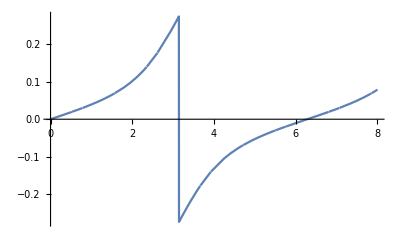

```mathematica
Plot[Re[indefiniteIntegral], {χprime, 0, 8}]
```

```mathematica
tEq=p^2 M√(p-2-2e) √(p-2+2e) indefiniteIntegral
```

793.725 (-(0.0222222 √(4.-1. Cos[χprime]) Sin[χprime])/(2.+1. Cos[χprime])-(0.0929516 √(-0.333333+0.333333 Cos[χprime]) √(1.+1. Cos[χprime]) (0.115741 Cos[2 χprime] Cos[3. χprime] EllipticE[1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+(-0.0925926 Cos[2. χprime] Cos[3 χprime]+0.115741 Cos[2 χprime] Cos[3. χprime]) EllipticF[1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.0625 Cos[χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+5.55112×10^-17 Cos[χprime] Cos[2. χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.146991 Cos[2. χprime] Cos[3 χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]-0.292824 Cos[2 χprime] Cos[3. χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.0625 Cos[5 χprime] EllipticPi[-0.75,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]-0.0629823 Cos[χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.00540123 Cos[2. χprime] Cos[3 χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]+0.00250772 Cos[2 χprime] Cos[3. χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]-0.0629823 Cos[5 χprime] EllipticPi[0.5,1. ArcSin[0.57735 √(4.-1. Cos[χprime])],0.6]) Sin[χprime])/(0.375 Cos[χprime]-1.625 Cos[χprime]^3+2.25 Cos[χprime]^5-1. Cos[χprime]^7))

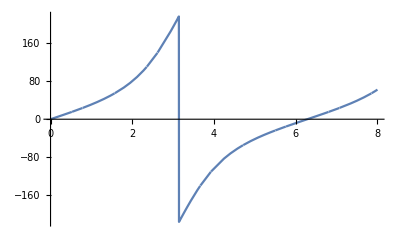

```mathematica
Plot[Re[tEq], {χprime, 0, 8}]
```

```mathematica
(* This is working... I think... It's extremely messy and I can't tell if the results just are or if something's wrong. I don't like the bad results at χ=nπ the slowness of the definite integrals is weird, slow to the point that I haven't even been able to compare indefinite-indefinite to one definite. 
I think the next steps are to clean this up and play around with it more to see what the t curves for different parameters look like and what kinds of different values I get. Definitely see if I can compare definite to two indefinites. Compare to the method from the other paper. Maybe hook it into a manipulate to see what the different parameters do, then just see if I can make that diagram Niels wanted and see what I run into and how it works out. *) 
(* AND PLAY AROUND WITH NIntegrate, I only just thought of it (shut up, I'm learning) and that could make all of this So Much easier *)
```

```mathematica
tEq/.χprime->π-0.00000005
```

301.798+81.949 ⅈ

```mathematica
Limit[tEq, χprime->π]
```

Indeterminate

```mathematica
(* Let's see if we can get the formulae from Kennefick's other paper up and running to compare the results. If they agree I'll still have questions but I'll be happy enough that its probably not Wrong. *)
```

```mathematica
(* Calculate the energy and angular momentum *)
En=√(((p-2-2e)(p-2+2e))/(p(p-3-e^2)))
L=√((p^2 M^2)/(p-3-e^2))

(* Define the terms they use in the second paper *)
a=0
x=L-a En
Vr=x^2+a^2+2a x En-(2M x^2)/p(3+e Cos[χ])
Vt=a^2 En-(2a M x)/p(1+e Cos[χ])+(En p^2)/(1+e Cos[χ])^2
J=1-(2M)/p(1+e Cos[χ])+a^2/p^2(1+e Cos[χ])^2
```

0.966092

3.849

0

3.849

14.8148-2.96296 (3+0.5 Cos[χ])

0.+96.6092/(1+0.5 Cos[χ])^2

1.-0.2 (1+0.5 Cos[χ])

```mathematica
integrand2002=Vt/(J √Vr)
indefinite2002=NIntegrate[integrand2002, {χ, 0, 2π}]
(*definite2002=Integrate[integrand2002, {χ, 0, 2}]*)
```

(0.+96.6092/(1+0.5 Cos[χ])^2)/((1.-0.2 (1+0.5 Cos[χ])) √(14.8148-2.96296 (3+0.5 Cos[χ])))

433.901

```mathematica
N[definite2002]
```

$Aborted

```mathematica
(* This cell above shows a problem I've had a few times. I ran it once (N[definite2002, 4]) and it gave me a solid answer (80.something) instantly. I ran it again (for precision = 5) and it buffered for ages, now any number I set it to (including back to 4) it takes forever. No clue what's going on. *)
(* Okay what the hell, I didn't specify the precision and it still won't run twice. *)
```